```mathematica
p0=Integrate[1/(1-x),{x, 0.52784376,x}]
```

ConditionalExpression[-0.750445-1. Log[1-x], Re[x]≤1.||x∉ℝ]

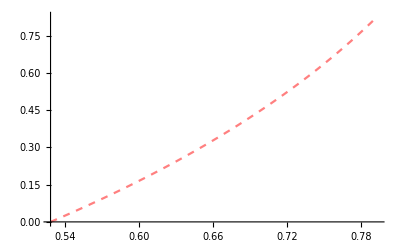

```mathematica
plt1=Plot[p0,{x,0.52784376,0.7936698080456}, PlotStyle->{Pink,Dashed}]
```

```mathematica
Solve[1-x-1.4634x^4==0,x]
```

{{x→-1.09367},{x→0.205589-0.934463 ⅈ},{x→0.205589+0.934463 ⅈ},{x→0.682492}}

```mathematica
Simplify[1/((x-(0.20558881956672903-0.934463314150207 ⅈ))(x-(0.20558881956672903+0.934463314150207 ⅈ)))]
```

1/((0.915488+0. ⅈ)-(0.411178+0. ⅈ) x+x^2)

```mathematica
pp1=Integrate[Apart[-1/(((0.9154884482234296+0. ⅈ)-(0.41117763913345806+0. ⅈ) x+x^2)(x+1.0936699870457531)(x-0.6824923479122948))],x]
```

0.566682 ArcTan[0.535066 (-0.411178+2. x)]-0.511522 Log[0.682492-1. x]+0.219815 Log[1.09367+1. x]+0.145854 Log[0.915488-0.411178 x+1. x^2]

```mathematica
pp10=pp1/.{x->0.47}
```

1.03826

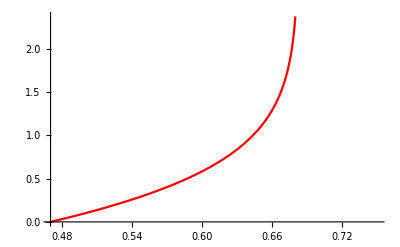

```mathematica
plt0=Plot[pp1-pp10,{x,0.47,0.75}, PlotStyle->Red]
```

```mathematica
Solve[1-x-0.52x^4==0,x]
```

{{x→-1.4774},{x→0.341865-1.23417 ⅈ},{x→0.341865+1.23417 ⅈ},{x→0.79367}}

```mathematica
Simplify[1/((x-(0.3418653013098282-1.2341733075456538 ⅈ))(x-(0.3418653013098282+1.2341733075456538 ⅈ)))]
```

1/((1.64006+0. ⅈ)-(0.683731+0. ⅈ) x+x^2)

```mathematica
pp2=Integrate[Apart[-1/(((1.6400556372978385+0. ⅈ)-(0.6837306026196563+0. ⅈ) x+x^2)(x+1.4774004106652632)(x-0.7936698080456067))],x]
```

0.227621 ArcTan[0.405129 (-0.683731+2. x)]-0.254917 Log[0.79367-1. x]+0.0911089 Log[1.4774+1. x]+0.0819041 Log[1.64006-0.683731 x+1. x^2]

```mathematica
pp20=pp2/.{x->0.52784376}
```

0.471482

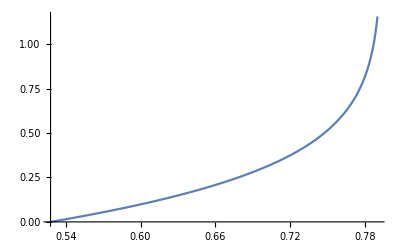

```mathematica
plt5=Plot[pp2-pp20,{x,0.52784376,0.79}]
```

```mathematica
NSolve[1-x-0.4x^4==0,x]
```

{{x→-1.59612},{x→0.388287-1.3268 ⅈ},{x→0.388287+1.3268 ⅈ},{x→0.819549}}

```mathematica
Simplify[1/((x-(0.38828696258785506-1.3268010518754596 ⅈ))(x-(0.38828696258785506+1.3268010518754596 ⅈ)))]
```

1/((1.91117+0. ⅈ)-(0.776574+0. ⅈ) x+x^2)

```mathematica
pp3=Integrate[Apart[1/(((1.9111677965735283+0. ⅈ)-(0.7765739251757101+0. ⅈ) x+x^2)(x+1.5961228374592809)(x-0.8195489122835696))],x]
```

-0.177784 ArcTan[0.376846 (-0.776574+2. x)]+0.212683 Log[0.819549-1. x]-0.0726471 Log[1.59612+1. x]-0.0700179 Log[1.91117-0.776574 x+1. x^2]

```mathematica
pp30=pp3/.{x->0.83}
```

-1.13854+0.668163 ⅈ

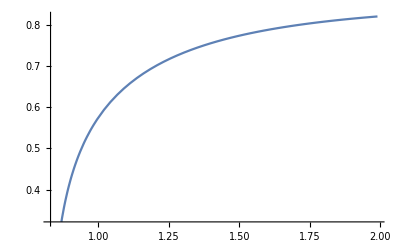

```mathematica
Plot[pp3-pp30,{x,0.83,1.99}]
```

```mathematica
Apart[1/(((1.9111677965735283+0. ⅈ)-(0.7765739251757101+0. ⅈ) x+x^2)(x+1.5961228374592809)(x-0.8195489122835696))]
```

0.212683/(-0.819549+1. x)-0.0726471/(1.59612+1. x)+(-0.181509-0.140036 x)/(1.91117-0.776574 x+1. x^2)

```mathematica
int1=Integrate[0.21268295383734906/(-0.8195489122835696+1. x),x]
```

0.212683 Log[0.819549-1. x]

```mathematica
0.21268295383734906 Log[-0.8195489122835696+1. x]
```

0.212683 Log[-0.819549+1. x]

```mathematica
int2=Integrate[-0.07264706004129193/(1.5961228374592809+1. x),x]
```

-0.0726471 Log[1.59612+1. x]

```mathematica
int3=Integrate[(-0.1815094913741448-0.14003589379605713 x)/(1.9111677965735283-0.7765739251757101 x+1. x^2),x]
```

-0.177784 ArcTan[0.376846 (-0.776574+2. x)]-0.0700179 Log[1.91117-0.776574 x+1. x^2]

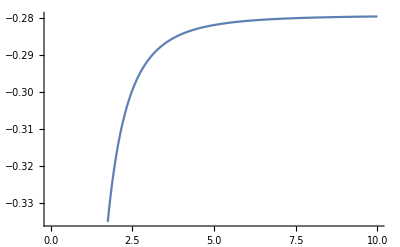

```mathematica
Plot[0.21268295383734906 Log[-0.8195489122835696+1. x]+int2+int3,{x,0,10}]
```

```mathematica
NSolve[1.2x^4+x==1,x]
```

{{x→-1.15803},{x→0.226783-0.984925 ⅈ},{x→0.226783+0.984925 ⅈ},{x→0.704462}}

```mathematica
pp0=p0/.{x->0.5925}
```

0.147269

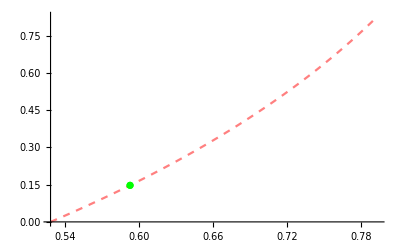

```mathematica
Show[plt1, ListPlot[{{0.5925,0.14726901507976742}}, PlotRange->All,PlotStyle->{Green}] ]
```

```mathematica
p33=Integrate[1/(0.7-x+4*1.22472*0.7^4(1-x/0.7)),{x,0.525,x}]
```

ConditionalExpression[0.37309 (-1.74297-1. Log[0.7-1. x]), Re[x]≤0.69999999999999995559||x∉ℝ]

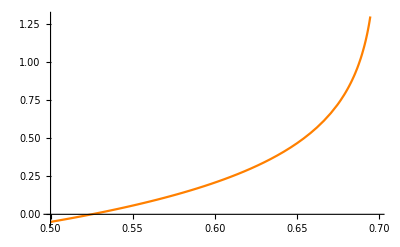

```mathematica
plt2=Plot[p33,{x,0.5,0.699}, PlotStyle->Orange]
```

```mathematica
int4=Integrate[1/((1+4*0.52*0.7936698080456067^3)(0.7936698080456067-x)),{x,0.5925,x}]
```

ConditionalExpression[-0.490225 ((1.60361-3.14159 ⅈ)+Log[-0.79367+x]), Re[x]≤0.79366980804560671725||x∉ℝ]

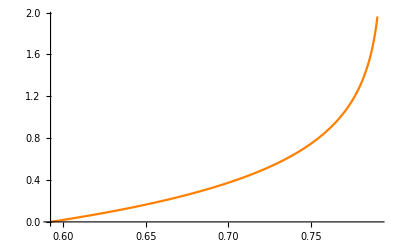

```mathematica
plt4=Plot[int4,{x,0.5925,0.79},PlotStyle->Orange]
```

```mathematica
prov1=int4/.{x->0.5925}
```

0.+0. ⅈ

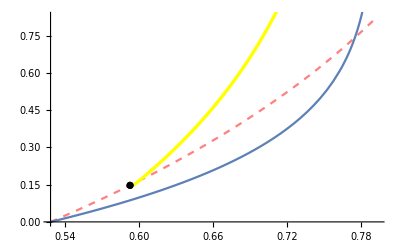

```mathematica
Show[plt1, ListPlot[{{0.5925,0.14726901507976742}}, PlotRange->All,PlotStyle->{Black, Thickness[0.1]}],prov2,plt5]
```

```mathematica
Simplify[(1.010035667357168-0.44902354093830715 x+x^2)(x+1.151236682252357)(x-0.7022131413140499)]
```

(-0.702213+x) (1.15124+x) (1.01004-0.449024 x+x^2)

```mathematica
Rationalize[1.4634]
```

7317/5000

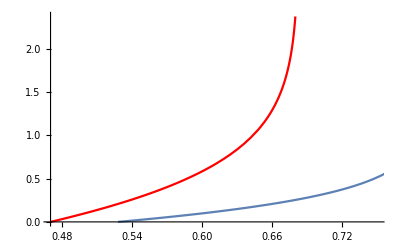

```mathematica
Show[plt0,plt5]
```

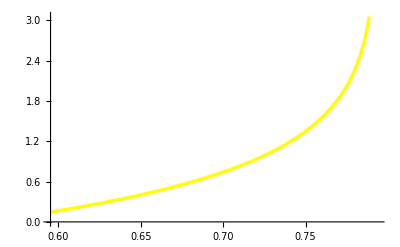

```mathematica
prov2=Plot[((-1)/(1+0.52*0.7936698080456067^3))*Log[4-4x/0.7936698080456067]+0.14726901507976742,{x,0.7936698080456067*0.75,0.7936698080456067}, PlotStyle->{Yellow, Thickness[0.006]}]
```

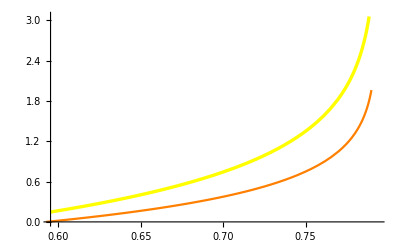

```mathematica
Show[prov2,plt4]
```

```mathematica
p5=Integrate[1/(1-x),{x, 1.5,x}]
```

ConditionalExpression[(-0.693147+3.14159 ⅈ)-1. Log[1-x], Re[x]>1.||x∉ℝ]

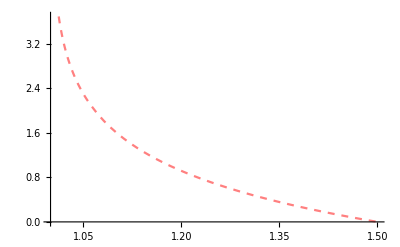

```mathematica
plt6=Plot[p5,{x,1.000001,1.5}, PlotStyle->{Pink,Dashed}]
```

```mathematica
pp7=Integrate[Apart[-1/(((1.6400556372978385+0. ⅈ)-(0.6837306026196563+0. ⅈ) x+x^2)(x+1.4774004106652632)(x-0.7936698080456067))],x]
```

0.227621 ArcTan[0.405129 (-0.683731+2. x)]-0.254917 Log[0.79367-1. x]+0.0911089 Log[1.4774+1. x]+0.0819041 Log[1.64006-0.683731 x+1. x^2]

```mathematica
pp70=pp7/.{x->1.76}
```

0.413703-0.800846 ⅈ

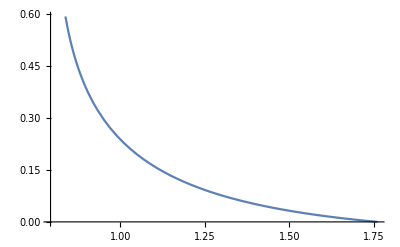

```mathematica
plt7=Plot[pp7-pp70,{x,0.7936698080456068,1.76}]
```

```mathematica
pp20=Integrate[1/(0.7936698080456067-x+0.52*0.7936698080456067^4((x-0.7936698080456067)*(1-(1.76/0.7936698080456067)^4)*(1/(1.76-0.7936698080456067)))),x]
```

-0.168073 Log[0.79367-1. x]

```mathematica
pp200=pp20/.{x->1.76}
```

0.00575645-0.528017 ⅈ

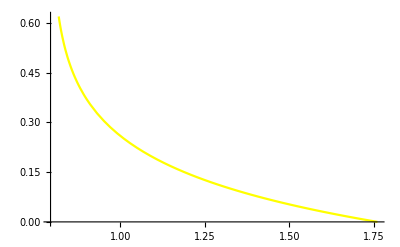

```mathematica
plt9=Plot[pp20-pp200,{x,0.7936698080456068,1.76}, PlotStyle->Yellow]
```

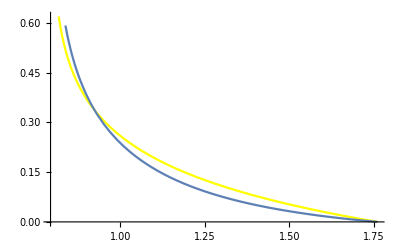

```mathematica
Show[plt9,plt7]
```